```mathematica
ClearAll["Global`*"]
```

```mathematica
xl=0;
xr=1;
```

```mathematica
(*test case 1*)
```

```mathematica
z[x_]:=x^4/48
```

```mathematica
z'[x]
```

x^3/12

```mathematica
D[z[x]z'[x],x]
```

(7 x^6)/576

```mathematica
D[D[z[x]z'[x],x],x]
```

(7 x^5)/96

```mathematica
D[D[D[z[x]z'[x],x],x],x]
```

(35 x^4)/96

```mathematica
u''[x]//FullSimplify
```

x^2/4

```mathematica
u''[x]//FullSimplify
```

(π^2 Cos[2 π x] (-187+344 Cos[4 π x]+388 Cos[8 π x]-24 Cos[12 π x]-9 Cos[16 π x]))/(32 (1+Cos[2 π x]^4)^3)

```mathematica
(*check for u*)
```

```mathematica
t=Import["/Users/michelecastellana/Documents/finite_elements/poisson_equation/solve_u/solution/nodal_values/u.csv"];
t=Table[{t[[i,2]],t[[i,1]]},{i,2,Length[t]}]
```

```mathematica
δ=Max[Table[Abs[t[[i,2]]-u[t[[i,1]]]],{i,1,Length[t]}]]
```

1.78178×10^-7

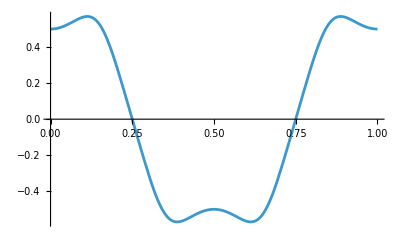

```mathematica
plotexact=Plot[u[x],{x,xl,xr},PlotRange->Full]
```

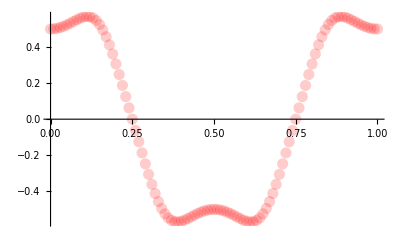

```mathematica
plotnum=ListPlot[t,PlotRange->Full,PlotStyle->{Red,Opacity[0.2],PointSize->0.02}]
```

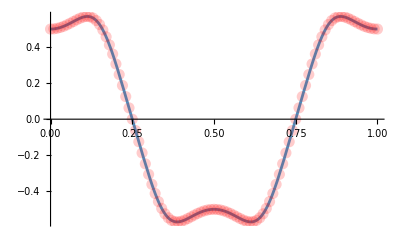

```mathematica
Show[plotexact,plotnum]
```